## Base model

```mathematica
mat={{rh-me,mh},{me,re-mh}}
```

{{-me+rh,mh},{me,-mh+re}}

```mathematica
mat//MatrixForm
```

(-me+rh | mh
me | -mh+re)

```mathematica
Eigensystem[mat]
```

{{1/2 (-me-mh+re+rh-√((me+mh-re-rh)^2-4 (-me re-mh rh+re rh))),1/2 (-me-mh+re+rh+√((me+mh-re-rh)^2-4 (-me re-mh rh+re rh)))},{{-(me-mh+re-rh+√(me^2+2 me mh+mh^2+2 me re-2 mh re+re^2-2 me rh+2 mh rh-2 re rh+rh^2))/(2 me),1},{-(me-mh+re-rh-√(me^2+2 me mh+mh^2+2 me re-2 mh re+re^2-2 me rh+2 mh rh-2 re rh+rh^2))/(2 me),1}}}

```mathematica
(*Largest eigenvalue*)
```

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

## Symmetric migration rates

```mathematica
Lambdaratio[Rr_,m_]:=Lambda[Rr,m,1,m]
```

### Sensitivity & Elasticity analysis

```mathematica
D[Lambdaratio[rho,m],rho]
```

1/2 (1+(-4 (1-m)-2 (-1+2 m-rho))/(2 √((-1+2 m-rho)^2-4 (-m+rho-m rho))))

```mathematica
FullSimplify[√((-1-rho+2 m)^2-4 (rho-m-rho m))]
```

√(4 m^2+(-1+rho)^2)

```mathematica
FullSimplify[-4 (1-m)-2 (-1-rho+2 m)]
```

2 (-1+rho)

```mathematica
DLambdaDrho[rho_,m_]:=1/2 (1+(-1+rho)/(√((-1+rho)^2+4 m^2)))
```

```mathematica
D[Lambdaratio[rho,m],m]
```

1/2 (-2+(-4 (-1-rho)+4 (-1+2 m-rho))/(2 √((-1+2 m-rho)^2-4 (-m+rho-m rho))))

```mathematica
FullSimplify[(-4 (-1-rho)+4 (-1-rho+2 m))/(2 √((-1-rho+2 m)^2-4 (rho-m-rho m)))]
```

(4 m)/(√(4 m^2+(-1+rho)^2))

```mathematica
DLambdaDt[rho_,m_]:=-1+(2 m)/(√((-1+rho)^2+4 m^2))
```

```mathematica
(*Equation for the equality of sensitivities*)
```

```mathematica
Solve[-1/2 (-2+(4 m)/(√((-1+rho)^2+4 m^2)))==1/2 (1+(2 (-1+rho))/(2 √((-1+rho)^2+4 m^2))),m]
```

{{m→0},{m→-2/3 (-1+rho)}}

```mathematica
(*FIGURE 1*)
```

```mathematica
(*FIGURE 1 - version sensitivity*)
```

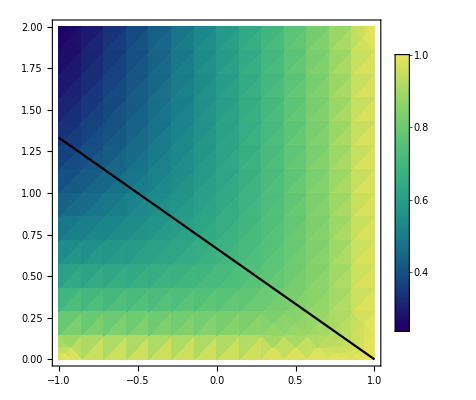

```mathematica
Show[DensityPlot[Lambdaratio[Rr,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.25,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle->Directive[Black,Thick]]]
```

## Asymmetric migration rates

```mathematica
LambdaratioAlpha2[Rr_,m_,alpha_]:=Lambda[Rr,m*alpha,1,m]
```

### Definition of the derivative functions

```mathematica
Simplify[D[LambdaratioAlpha2[rho,m,alpha],rho]]
```

1/4 (2+(2 (-1+(-1+alpha) m+rho))/(√((-1+m+alpha m-rho)^2+4 (m-rho+alpha m rho))))

```mathematica
DLDRAL2[rho_,m_,alpha_]:=1/4 (2+(2 (-1+(-1+alpha) m+rho))/(√((-1+m+alpha m-rho)^2+4 (m-rho+alpha m rho))))
```

```mathematica
Simplify[D[LambdaratioAlpha2[rho,m,alpha],m]]
```

1/2 (-1-alpha+(1+m+alpha^2 m-rho+alpha (-1+2 m+rho))/(√((-1+m+alpha m-rho)^2+4 (m-rho+alpha m rho))))

```mathematica
DLDTAL2[rho_,m_,alpha_]:=1/2 (-1-alpha+(1+m+alpha^2 m-rho+alpha (-1+2 m+rho))/(√((-1+m+alpha m-rho)^2+4 (m-rho+alpha m rho))))
```

### Plot elasticities

```mathematica
listalpha = {0.1,0.25,0.5,0.75,1,1.5,2,3,4,7}
```

{0.1,0.25,0.5,0.75,1,1.5,2,3,4,7}

```mathematica
listcolor=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[listalpha]-1)}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2641351111111111, 0.20142911111111111, 0.7458891111111111],RGBColor[0.2563255555555556, 0.4309208888888889, 0.8085534444444444],RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334],RGBColor[0.4391281111111111, 0.7049679999999999, 0.52925],RGBColor[0.5971805555555556, 0.7421848888888889, 0.36770955555555557],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.8801795555555555, 0.6316843333333333, 0.22766533333333333],RGBColor[0.8973538888888889, 0.4182404444444444, 0.18500666666666665],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
(*In figure 1*)
```

### Plot sensitivities

```mathematica
(*In this case we can solve analytically the equality of sensitivities*)
```

```mathematica
Solve[DLDRAL2[rho,m,alpha]==-DLDTAL2[rho,m,alpha],m]
```

{{m→0},{m→-(2 (-1+rho))/(2+alpha)}}

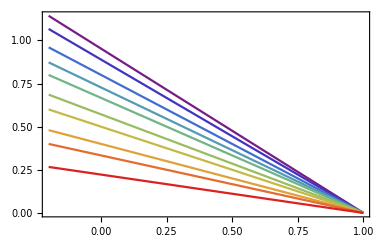

```mathematica
Show[Table[Plot[-(2 (-1+rho))/(2+alpha)/.alpha->listalpha[[i]],{rho,-0.2,1},PlotStyle->listcolor[[i]],LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold},Frame->True],{i,1,Length[listalpha]}]]
```

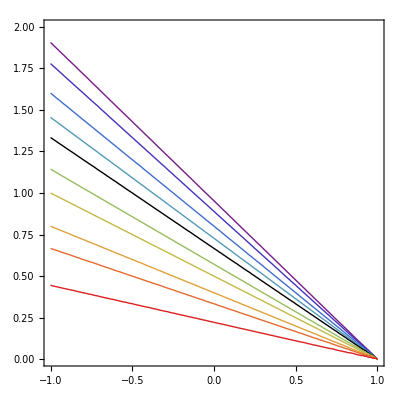

```mathematica
Show[Table[ContourPlot[Abs[DLDTAL2[rho,m,listalpha[[ialpha]]]/DLDRAL2[rho,m,listalpha[[ialpha]]]],{rho,-1,1},{m,0.00001,2.2},ContourShading->None,Contours->{1}, ContourStyle->listcolor[[ialpha]],BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold},PlotRange->{{-1,1},{0,2}}],{ialpha,1,4}],ContourPlot[Abs[DLDTAL2[rho,m,1]/DLDRAL2[rho,m,1]],{rho,-1,1},{m,0.00001,2.2},ContourShading->None,Contours->{1.0}, ContourStyle->Directive[Black,Thick],PlotRange->All],Table[ContourPlot[Abs[DLDTAL2[rho,m,listalpha[[ialpha]]]/DLDRAL2[rho,m,listalpha[[ialpha]]]],{rho,-1,1},{m,0.00001,1.5},ContourShading->None,Contours->{1}, ContourStyle->listcolor[[ialpha]],BaseStyle->{FontSize->16},PlotRange->All],{ialpha,6,Length[listalpha]}]]
```